## Configurations and Equations

### Field Configuration

#### Unit conversions

```mathematica
λToω[λ_]:=2π (0.052918 ×137)/λ
```

```mathematica
ωToλ[ω_]:=2π (0.052918 ×137)/ω
```

#### fieldConfig

```mathematica
fieldConfig::usage = "fieldConfig[] is a protected variable, which will act to hold an association of all its defining components, e.g., the time-dependence, wavelength, intensity";
Protect[fieldConfig];
(*this is the container (struct) where I can put all the field information into*)
```

#### fcSymbolic

```mathematica
fcSymbolic=fieldConfig["E1"->E1,"E2"->E2,"E0"->E0,"ϕ1"->ϕ1,"ϕ2"->ϕ2,"r"->1,"s"->2,"ω"->ω];
```

```mathematica
fcSymbolicToStrings={E1->"E1",E2->"E2",E0->"E0",ϕ1->"ϕ1",ϕ2->"ϕ2",ω->"ω"};
```

#### fcStrings

```mathematica
fcStrings=fieldConfig["E1"->"E1","E2"->"E2","E0"->"E0","ϕ1"->"ϕ1","ϕ2"->"ϕ2","r"->1,"s"->2,"ω"->"ω"];
```

#### makeFieldConfig

```mathematica
makeFieldConfig["E1"->E1_,"E2"->E2_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_]:=fieldConfig[
"E1"->E1,
"E2"->E2,
"E0"->E0,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,
"ω"->ω]
(* this shall generate a fieldConfig that can then be used for further computation of the field, the potential, the action etc. *)
```

I can overload this with a lot of definitions, e.g. income intensity etc

```mathematica
makeFieldConfig["E1"->E1_,"θ"->θ_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_]:=fieldConfig[
"E1"->Cos[θ]E1,
"E2"->Sin[θ]E1,
"E0"->E0,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,
"ω"->ω]
```

```mathematica
makeFieldConfig["θ"->θ_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_]:=fieldConfig[
"E1"->Cos[θ]1,
"E2"->Sin[θ]1,
"E0"->E0,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,
"ω"->ω]
```

```mathematica
makeFieldConfig["ampratio"->ampratio_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_]:=fieldConfig[
"E1"->1,
"E2"->ampratio × 1,
"E0"->E0,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,
"ω"->ω]
```

```mathematica
makeFieldConfig["R"->R_,"Intensity"->Intensity_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_]:=fieldConfig[
"E1"->1/(√(1+R^2)),
"E2"->R/(√(1+R^2)),
"E0"->Sqrt[Intensity/(3.5×10^16)],
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,
"ω"->ω]
```

```mathematica
ampRatioToMixingAngleθ[ampratio_]:=ArcTan[ampratio] (*because ampratio = Sin[θ]/Cos[θ]=Tan[θ]*)
```

```mathematica
ampRatioToMixingAngleθ[0.29]
```

0.282257

```mathematica
(Tan^2)[θ]//Simplify
```

Tan^2[θ]

#### test configuration

```mathematica
testfieldconfig=makeFieldConfig["E1"->1,
"θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800]]
```

fieldConfig[E1→1/(√2),E2→1/(√2),E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395]

```mathematica
testfieldconfigfold=makeFieldConfig["E1"->1,
"θ"->0.33,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800]]
```

fieldConfig[E1→0.946042,E2→0.324043,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395]

### calculate the strong-field parameter

```mathematica
zfFromConfig[fieldConfig_]:=("E0")^2/("ω")^3/.(Association@@fieldConfig)
```

```mathematica
zfFromConfig[fieldConfig_,"Updirect"]:=UpondFromConfig[fieldConfig]/("ω")/.(Association@@fieldConfig)
```

```mathematica
zfFromConfig[testfieldconfig,2]
```

27.5544

```mathematica
zfFromConfig[testfieldconfig]
```

61.9085

### Target

```mathematica
targetConfig::usage = "targetConfig is a protected variable, which will hold the value for the ionization potential (as this is the only defining quantity for now)";
Protect[targetConfig];
```

#### κFromConfig

```mathematica
κFromConfig[targetConfig_]:= √(2 "Ip")/.(Association@@targetConfig)
```

#### Test target

```mathematica
testtargetconfig=targetConfig["Ip"->0.5] (*Hydrogen*)
```

targetConfig[Ip→0.5]

### ponderomotive energy (Upond)

```mathematica
UpondFromConfig[fieldConfig_]:=1/(2 π) ×Integrate[
potentialFromConfig[fieldConfig][ωt]*potentialFromConfig[fieldConfig][ωt],
{ωt,0,2 π}]
```

```mathematica
(*OLD DEFINITION OF UPOND:
 A01=-1/(√(1+R^2))E0/ω; A02=1/(√(1+R^2)) R E0/ω;
Upond=(A01^2/4+A02^2/4)/. config;
Return[Upond/. R->Rx]
As in, usually Upond = (E0/(2ω))^2. *)
```

```mathematica
1/(2 π)Integrate[potentialFromConfig[testfieldconfig][wt]*potentialFromConfig[testfieldconfig][wt],{wt,0,2 π}]
```

1.56893

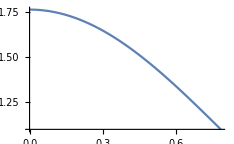

```mathematica
Plot[UpondFromConfig[fastFieldConfigθ[θx]],{θx,0,π/4}]
```

pmax should be:

```mathematica
2 UpondFromConfig[fastFieldConfigθ[0]]
```

3.52504

### Keldysh parameter

```mathematica
KeldyshγFromConfig[fieldConfig_,targetConfig_]:=Sqrt[("Ip"/.(Association@@targetConfig))/(2 UpondFromConfig[fieldConfig])]
```

```mathematica
KeldyshγFromConfig[fieldConfig_,targetConfig_,"Upfixed"]:=Sqrt[("Ip"/.(Association@@targetConfig))/(2 (("E0")/("ω"))^2/.(Association@@fieldConfig))]
```

### Cheat Functions for quick mixing angle configs

```mathematica
fastFieldConfigθ[θx_]:=makeFieldConfig["E1"->1,
"θ"->θx,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800]]
```

### Get the field equation, vector potential and action

#### Field

```mathematica
fieldFromConfig[fieldConfig_][ωt_]:=Module[{f,fun},
f=Association@@fieldConfig;

"E1" "E0" Sin["r" ωt + "ϕ1"]+"E2" "E0" Sin["s" ωt+"ϕ2"]/.f

]
```

?? ? WHY DOES THIS NOT WORK THE WAY I WANT??? WHAT DO I WANT????

```mathematica
fieldFromConfig[]:=fieldFromConfig[fcSymbolic]
```

```mathematica
fieldFromConfig[ωt_]:=fieldFromConfig[fcSymbolic][ωt]
```

```mathematica
fcSymbolic
```

fieldConfig[E1→E1,E2→E2,E0→E0,ϕ1→ϕ1,ϕ2→ϕ2,r→1,s→2,ω→ω]

```mathematica
fieldFromConfig[x_]:=Block[{f},
f[y]=fieldFromConfig[fcSymbolic][y];
f[x]

]
```

```mathematica
fieldFromConfig[]
```

fieldFromConfig[fieldConfig[E1→E1,E2→E2,E0→E0,ϕ1→ϕ1,ϕ2→ϕ2,r→1,s→2,ω→ω]]

```mathematica
fieldFromConfig[fcSymbolic][z]/.z->2
```

E0 E1 Sin[2+ϕ1]+E0 E2 Sin[4+ϕ2]

```mathematica
ClearAll[fieldFromConfig]
```

#### Potential

```mathematica
potentialFromConfig[fieldConfig_][ωt_]:=Module[{f,fun,field,pot,intfactor},
intfactor=1/("ω")/.(Association@@fieldConfig);
field[x_]=fieldFromConfig[fieldConfig][x] ;

-intfactor×Integrate[field[x],x]/.x->ωt
]
```

```mathematica
potentialFromConfig::usage="potentialFromConfig[fieldConfig] takes in a valid fieldConfig object and returns a vector potential A as a Function object, where A[t] is a numeric (or symbolic) vector potential";
```

```mathematica
(*potential[field_][ωt_]:=Module[{},
Print[Function[x,field]];
-Integrate[field[x],x]/.x->ωt
]*) (*THIS DOESN'T WORK*)
```

```mathematica
potentialFromConfig[testfieldconfig][d]
```

-17.5625 (0.0755929 Sin[d]-0.0377964 Sin[2. d])

```mathematica
ClearAll[potentialFromConfig]
```

#### Action

```mathematica
action[p_,ωt_]=Module[{f,fun,field,pot,IntPot,IntPotsq},
field=fieldFromConfig[fcSymbolic][ωt];
pot=potentialFromConfig[fcSymbolic][ωt];
IntPot=Integrate[pot,ωt];
IntPotsq=Integrate[pot*pot,ωt];

(1/2 (p^2 ωt +2 p IntPot+IntPotsq) +1/2 κ^2 ωt)
]
```

(κ^2 ωt)/2+1/2 (p^2 ωt+2 p ((E0 E1 Cos[ωt] Sin[ϕ1])/ω+(E0 E2 Cos[2 ωt] Sin[ϕ2])/(4 ω)+(E0 E1 Cos[ϕ1] Sin[ωt])/ω+(E0 E2 Cos[ϕ2] Sin[2 ωt])/(4 ω))+(E0^2 (2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ϕ1-ϕ2-ωt]+E1^2 Sin[2 (ϕ1+ωt)]+1/8 E2^2 Sin[2 (ϕ2+2 ωt)]+2/3 E1 E2 Sin[ϕ1+ϕ2+3 ωt]))/(4 ω^2))

```mathematica
actionFromConfig[fieldConfig_,targetConfig_][p_,ωt_]:=Module[{f,fun,field,pot,IntPot,IntPotsq},
f=Association@@fieldConfig;

action[p,ωt]/.fcSymbolicToStrings/.f/.κ->κFromConfig[targetConfig]

]
```

```mathematica
OLD actionFromConfig[fieldConfig_,targetConfig_][p_,ωt_]:=Module[{f,fun,field,pot,IntPot,IntPotsq,κ},
f=Association@@fieldConfig;
field[x_]=fieldFromConfig[fieldConfig][x];
pot[x_]=potentialFromConfig[fieldConfig][x];
(*pot[x_]=potential[field][x];*)
IntPot[xx_]=Integrate[pot[x],x]/.x->xx;
IntPotsq[xx_]=Integrate[pot[x]*pot[x],x]/.x->xx;
κ=κFromConfig[targetConfig];

Function[{px,x},
(1/2 (px^2 x +2 px IntPot[x]+IntPotsq[x]) +1/2 κ^2 x)
][p,ωt]  

(* there's almost certainly a way to write this better #mathematicadyslexia *)

]
```

```mathematica
actionFromConfig[testfieldconfig,testtargetconfig][d,t]
```

0.5 t+1/2 (d^2 t+2 d (0.+1.3276 Cos[t]-0.3319 Cos[2 t])+0.88126 ((5 t)/4-Sin[t]+1/3 Sin[3 t]+1/2 Sin[2 (π/2+t)]+1/16 Sin[2 (-π/2+2 t)]))

```mathematica
ClearAll[actionFromConfig]
```

### Derivatives of the action

```mathematica
dSdωt[fieldConfig_,targetConfig_][p_,ωt_]:=Module[{drv},
drv[px_,x_]=D[actionFromConfig[fieldConfig,targetConfig][px,x],x];

Function[{px,x},
drv[px,x]
][p,ωt]

]
```

```mathematica
d2Sdωt2[fieldConfig_,targetConfig_][p_,ωt_]:=Module[{drv2},
drv2[px_,x_]=D[actionFromConfig[fieldConfig,targetConfig][px,x],{x,2}];

Function[{px,x},
drv2[px,x]
][p,ωt]

]
```

```mathematica
ClearAll[dSdωt]
```

## Finding Critical Points

### Checking the boundaries for the saddle point search and classification

#### OLD Field (old)

```mathematica
DynamicModule[{potential,Efield1,Efield2,Efield,A0=1, E0=1,saddlesp0,saddlesp05,saddlespm05},
potential=potA[ωt,θ,"X"]/.A0->1;
Efield1=E0 Cos[θ] Cos[ωt] ;
Efield2=-E0 Cos[2 ωt] Sin[θ];
Efield=E0 Cos[θ] Cos[ωt]-E0 Cos[2 ωt] Sin[θ];

Manipulate[
saddlesp0=FindSaddles[θx,0,"X"];
saddlesp05=Select[FindSaddles[θx,0.5,"X"],Im[#]<=π &];
saddlespm05=Select[FindSaddles[θx,-0.5,"X"],Im[#]<=π&];

Show[{Plot[{Efield1/.θ->θx, Efield2/.θ->θx,Efield/.θ->θx,potential/.θ->θx}
,{ωt,-π,2π}
, PlotStyle->{Directive[Dashed,Red],Directive[Dashed,Blue],Directive[Thick,Black],Directive[Green]}
, PlotLegends->{"E1","E2","combined field","potential"}
,GridLines->{{-3/5 π,2/3 π,2π-3/5 π,3/5 π},None}
,PlotRange->{{-π,2π},{-1.5,1}}
],
ListPlot[{Re[#],Efield/.{ωt->Re[#],θ->θx}}&/@saddlesp0,PlotStyle->Black,PlotMarkers->{Automatic,8}]
,
ListPlot[{Re[#],Efield/.{ωt->Re[#],θ->θx}}&/@saddlesp05
,PlotStyle->Red,PlotMarkers->{Automatic,8}
],
ListPlot[{Re[#],Efield/.{ωt->Re[#],θ->θx}}&/@saddlespm05
,PlotStyle->Blue,PlotMarkers->{Automatic,8}
]
}]
,{{θx,0.2},0,π/2}
]
]
```

#### Trouble Shooting

```mathematica
testfieldconfig1=makeFieldConfig["E1"->1,
"θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,"r"->1,"s"->2,
"ω"->λToω[300]];
```

```mathematica
testlastsaddle=(findSaddles[testfieldconfig1,testtargetconfig][-4])
```

{-2.0944,0.,2.0944}

{0.560455+1.88804 ⅈ,0.774051+1.8608 ⅈ,3.90478+1.60827 ⅈ,4.1855+1.63552 ⅈ}

```mathematica
4.185495498104671+1.63551861672977 ⅈ-2π
```

-2.09769+1.63552 ⅈ

```mathematica
findωtMin[testfieldconfig1]
```

{-2.0944,0.,2.0944}

-2.0944

```mathematica
2 UpondFromConfig[testfieldconfig1]
```

0.309818

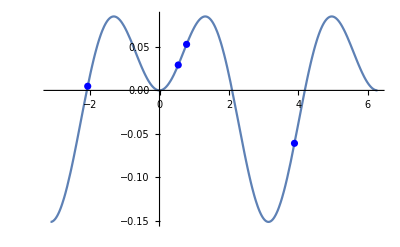

```mathematica
Show[{
Plot[fieldFromConfig[testfieldconfig1][ωt],{ωt,-π,2π}],
ListPlot[{Re[#],fieldFromConfig[testfieldconfig1][Re[#]]}&/@findSaddles[testfieldconfig1,testtargetconfig][-3.5],PlotStyle->Blue]
(*,ListPlot[{Re[#],fieldFromConfig[testfieldconfig1][Re[#]]}&/@findSaddles[testfieldconfig1,testtargetconfig][4],PlotStyle->Red]*)
}]
```

#### findωtBorder[]: Finding the border between the two bands

```mathematica
findωtBorder[fieldConfig_]:=
Module[{borderrange,bordertime,zeros},
borderrange={π/2,(3π)/4};
zeros=Select[ωt/.
Quiet@NSolve[
fieldFromConfig[fieldConfig][ωt]
==0,ωt]/.C[1]->{0,1}//Flatten
, Abs[Im[#]]<10^-5&];
bordertime=Select[zeros, borderrange[[1]]<=Re[Round[#,10^-5]]<=borderrange[[2]]&][[1]];
Return[bordertime]
]
```

```mathematica
findωtBorder[testfieldconfig]
```

2.0944

### Grid of seeds

```mathematica
SeedsGrid[fieldConfig_]:=Module[{},
(*Print[fieldConfig];*)
Flatten[Table[
ωtreal0+ⅈ ωtimag0,
{ωtreal0,-π,7/5 π,1},
{ωtimag0,0,If[(Association@@fieldConfig)[["E1"]]!=0 && (*I added this bc I don't want to divide by zero. I think it's not the best way to do it though*)
((Association@@fieldConfig)[["E2"]])/((Association@@fieldConfig)[["E1"]])<0.1,5π,6/5 π],0.5}
],1]
]
```

### Saddle Points (dSdωt = 0): FindSaddles()

```mathematica
findSaddles[fieldConfig_,targetConfig_][px_]:=
(*findSaddles[fieldConfig,targetConfig][px]=*)
Module[{allsolutions,solutions,seeds,ωtmin},
seeds=SeedsGrid[fieldConfig];
allsolutions = Block[{},Table[ωtx/.
Quiet@FindRoot[
dSdωt[fieldConfig,targetConfig][px,ωtx]==0,
{ωtx,ωtSeed}],
{ωtSeed,seeds}
]];
DeleteCases[solutions,{}];
solutions=DeleteDuplicates[Flatten[allsolutions,1], Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
solutions=Select[solutions,Abs[dSdωt[fieldConfig,targetConfig][px,#]]<10^-5&];

solutions=Select[solutions,And[Im[#]>0,-π<=Re[#]<2π]&];
(*Print[solutions];*)
solutions=SortBy[solutions,Re[#]&];
Return[solutions]
]
```

```mathematica
findSaddles::usage="findSaddles[fieldConfig_,targetConfig_][px_] searches for solutions of the first derivative of the action within -π and 2π. It return a list of phase values, ordered by their real part, which can then be sorted by the classification functions";
```

```mathematica
findSaddles[testfieldconfig1,testtargetconfig][-4]
```

{-2.37841+1.60827 ⅈ,-2.09769+1.63552 ⅈ,-2.37841-1.60827 ⅈ,0.774051-1.8608 ⅈ,0.774051+1.8608 ⅈ,0.560455+1.88804 ⅈ,-2.09769-1.63552 ⅈ,3.90478-1.60827 ⅈ,3.90478+1.60827 ⅈ,4.1855+1.63552 ⅈ}

{0.560455+1.88804 ⅈ,0.774051+1.8608 ⅈ,3.90478+1.60827 ⅈ,4.1855+1.63552 ⅈ}

```mathematica
findSaddles[testfieldconfig,testtargetconfig][0.1]//AbsoluteTiming
```

{4.56976,{-0.92037+0.729488 ⅈ,-0.029701+1.04967 ⅈ,0.982392+0.677822 ⅈ,3.10927+0.357641 ⅈ}}

### makeFieldConfigForAmpRatio[fieldConfig_, ampratio]

```mathematica
ClearAll[makeFieldConfigForAmpRatio]
```

```mathematica
(*makeFieldConfigForAmpRatio2[fieldConfig_,ampratio_]:=
makeFieldConfigForAmpRatio2[fieldConfig,ampratio]=
Module[{assoc},
(*Print["here!",Head[ampratio]];*)
(*Print["here again! ",Head[N[ampratio]]];*)
assoc=Association@@fieldConfig;
(*assoc[["E2"]]=ampratio × assoc[["E1"]];*)
assoc[["E1"]]=1;
assoc[["E2"]]=N[ampratio] × 1;
(*Print[assoc[["E2"]]];*)
Return[
makeFieldConfig@@Normal[assoc]
]
]*)
```

```mathematica
makeFieldConfigForAmpRatio[fieldConfig_,ampratio_]:=
(*makeFieldConfigForAmpRatio[fieldConfig,ampratio]=*)
Module[{assoc},
(*Print["here2!",Head[ampratio]];*)
(*Print["here again! ",Head[N[ampratio]]];*)
assoc=Association@@fieldConfig;
(*assoc[["E2"]]=ampratio × assoc[["E1"]];*)
assoc[["E1"]]=1;
assoc[["E2"]]=N[ampratio] × 1;
(*Print[assoc[["E2"]]];*)
Return[
makeFieldConfig@@Normal[assoc]
]
]
```

### FoldPoint (dSdωt = d2Sdωt2 = 0)

```mathematica
(*den Test fuer R∈Reals habe ich hinzugefuegt, damit die Suche nach Stokes Transitions funktioniert. FindRoot(f(ampratio)) versucht sonst alles symbolisch zu loesen.*)
```

```mathematica
ClearAll[makeFieldConfigForAmpRatio]
```

```mathematica
Options[findFoldPoint]={OutputParameter->"ampratio"};Protect[OutputParameter];OutputParameter::usage="This is an option for findFoldPoint that specifies if we want to get the results in terms of an amplitude ratio ('ampratio',  E_2/E_1) or mixing angle ('mixingangle', θ=Tan[E_2/E_1]).";
findFoldPoint::UnknownOptionValue="The option you chose is currently not available";
```

```mathematica
ClearAll[findFoldPoint]
```

```mathematica
findFoldPoint[fieldConfig_,targetConfig_,OptionsPattern[]]:=
(*findFoldPoint[fieldConfig,targetConfig,OptionsPattern[]]=*)
Module[{px=0,allsolutions,solutions,seeds,ampratio,educatedseeds,ampratiofold,fold},
(*seeds=Union[SeedsGrid[makeFieldConfigForAmpRatio[fieldConfig,0]],SeedsGrid[makeFieldConfigForAmpRatio[fieldConfig,2]]];*)
educatedseeds=Flatten[Table[
ωtreal0+ⅈ ωtimag0,
{ωtreal0,-π/3,π/3,π/3},
{ωtimag0,0,π,π/2}
],1];
seeds={0+1ⅈ,0+2ⅈ}; (*wenn ich das hier direkt hinschreibe, dann muss ich unten auch die bounds nochmal anpassen!*)
(*educatedseeds;*)

allsolutions = Block[{},
Table[{ampratio,ωt}/.
Quiet@FindRoot[
{dSdωt[makeFieldConfigForAmpRatio[fieldConfig,ampratio],targetConfig][px,ωt]==0,
d2Sdωt2[makeFieldConfigForAmpRatio[fieldConfig,ampratio],targetConfig][px,ωt]==0},
{{ωt,ωtSeed},{ampratio,ampratio0}}],
{ampratio0,0.05,0.5,0.2},(*in doubt, this could be extended as well!*)
{ωtSeed,seeds}
]];

solutions=DeleteDuplicates[Flatten[allsolutions,1], Function[{p1,p2},And[Abs[p1[[1]]-p2[[1]]]<10^-5, Abs[p1[[2]]-p2[[2]]]<10^-5]]];
(*Print[solutions];*)
solutions=Select[solutions,And[
0<=Re[#[[1]]]<=1, (*bounds for ampratio*)
Im[#[[2]]]>0,
-0.5<=Re[#[[2]]]<0.5
(*Min[Re[seeds]]<=Re[#[[2]]]<Max[Re[seeds]]*)
]&];
(*Print[solutions];*)
 (*make sure that it  actually solves the second drv*)
solutions=Select[solutions,
Abs[
d2Sdωt2[makeFieldConfigForAmpRatio[fieldConfig,#[[1]]],targetConfig][px,#[[2]]]]
<10^-5&];

DeleteCases[solutions,{}];

ampratiofold=Re[solutions[[1,1]]];
fold=Which[
OptionValue[OutputParameter]=="ampratio","R"->ampratiofold,
OptionValue[OutputParameter]=="mixingangle","θ"->ampRatioToMixingAngleθ[ampratiofold],
True,Message[findFoldPoint::UnknownOptionValue]];

Return[<|"Order"->12,"ωt"->solutions[[1,2]],"p"->px,fold|>]
]
```

```mathematica
findFoldPoint[testfieldconfig,testtargetconfig,OutputParameter->"mixingangle"]//AbsoluteTiming
```

{0.804595,<|Order→12,ωt→0.+1.11168 ⅈ,p→0,θ→0.345905|>}

```mathematica
findFoldPoint[testfc300,testtargetconfig,OutputParameter->"mixingangle"]//AbsoluteTiming
```

{0.801352,<|Order→12,ωt→0.+1.818 ⅈ,p→0,θ→0.164999|>}

```mathematica
findFoldPoint[testfc3000,testtargetconfig,OutputParameter->"mixingangle"]//AbsoluteTiming
```

{0.786717,<|Order→12,ωt→0.+0.599127 ⅈ,p→0,θ→0.580136|>}

```mathematica
testfoldR=findFoldPoint[testfieldconfig,testtargetconfig,OutputParameter->"ampratio"][["R"]]
```

0.360394

### Troubleshooting

#### testfc for other wavelength

```mathematica
testfc300=makeFieldConfig["E1"->1,
"θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,"r"->1,"s"->2,
"ω"->λToω[300]];
```

```mathematica
testfc3000=makeFieldConfig["E1"->1,
"θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,"r"->1,"s"->2,
"ω"->λToω[3000]];
```

#### test findfold

```mathematica
Block[{px=0,allsolutions,solutions,seeds,ampratio,educatedseeds,ampratiofold,fold,fc},
(*seeds=Union[SeedsGrid[makeFieldConfigForAmpRatio[fieldConfig,0]],SeedsGrid[makeFieldConfigForAmpRatio[fieldConfig,2]]];*)
fc=makeFieldConfig["E1"->1,
"θ"->0.3,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,"r"->1,"s"->2,
"ω"->λToω[800]];

educatedseeds=Flatten[Table[
ωtreal0+ⅈ ωtimag0,
{ωtreal0,-π/3,π/3,π/3},
{ωtimag0,0,π,π/2}
],1];
seeds=educatedseeds;

(*allsolutions = Block[{},
Table[{ampratio,ωt}/.
Quiet@FindRoot[
{dSdωt[makeFieldConfigForAmpRatio[fc,ampratio],testtargetconfig][px,ωt]==0,
d2Sdωt2[makeFieldConfigForAmpRatio[fc,ampratio],testtargetconfig][px,ωt]==0},
{{ωt,ωtSeed},{ampratio,ampratio0}}],
{ampratio0,0.05,0.5,0.2},(*in doubt, this could be extended as well!*)
{ωtSeed,seeds}
]]*)

allsolutions = Block[{},
Table[
ampratio/.
Quiet@FindRoot[
{dSdωt[makeFieldConfigForAmpRatio[fc,ampratio],testtargetconfig][px,ωt]==0,
d2Sdωt2[makeFieldConfigForAmpRatio[fc,ampratio],testtargetconfig][px,ωt]==0},
{{ωt,0+1.1ⅈ},{ampratio,ampratio0}}],
{ampratio0,0.05,0.5,0.2}(*in doubt, this could be extended as well!*)
]]

]//AbsoluteTiming
```

{0.369003,{0.360394+0. ⅈ,0.360394+0. ⅈ,0.360394+0. ⅈ}}

## Classification

### ClassifySaddles() Functions

#### ClassifySaddles()

```mathematica
(*classifySaddles[fieldConfig_][saddlesList_]:=classifySaddles[fieldConfig][saddlesList,"ω"];*)
```

```mathematica
classifySaddles::missingArgument="Hey you! If you want to classify using the '2ω' scheme you need to provide the targetConfig as well!";

classifySaddles[fieldConfig_][saddlesList_,"2ω"]:=Message[classifySaddles::missingArgument]
```

#### ω-centric : ClassifySaddles() (“vertical”)

```mathematica
classifySaddles[fieldConfig_][saddlesList_,"ω"]:=Module[{
saddles,
ABCsaddles,
ABCsaddlesclassified,Dsaddle,
classifiedsaddles,
ωtmin,ωtborder,test,nsaddles1cycle,
myπ
},
(*ωtmin=findωtMin[fieldConfig];*)
ωtborder=findωtBorder[fieldConfig];
(*Print[ωtborder];*)
saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];
(*Print["saddles: ",Round[Re[#],0.01]&/@saddles];*)

myπ=Round[π,0.01];

nsaddles1cycle=Length[
Select[saddles,-myπ<Round[Re[#],0.01]<=myπ&]
];
(*Print[nsaddles1cycle];*)
Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{},
ABCsaddles=
SortBy[
saddles[[1;;3]],
Round[{Im[#],-Abs[Re[#]]},10^-5]&];
Dsaddle=Select[saddles[[4;;-1]],ωtborder<Re[#]&][[1]]
],
nsaddles1cycle<3,
Block[{},
ABCsaddles={saddles[[1]]};
(*Print["check1: ", Select[saddles[[2;;-1]],ωtborder<Re[#]&]];*)
Dsaddle=Select[saddles[[2;;-1]],ωtborder<Re[#]&][[1]]
],
nsaddles1cycle==3,
Block[{},
ABCsaddles=saddles[[1;;2]];
(*Print["check1: ", Select[saddles[[2;;-1]],ωtborder<Re[#]&]];*)
Dsaddle=Select[saddles[[3;;-1]],ωtborder<Re[#]&][[1]]
]
];

ABCsaddlesclassified=Table[
{ABCsaddles[[n]],{"A","C","B"}[[n]]},
{n,1,Length[ABCsaddles]}]; 

(*this is because at the coalescence we have only one SP under B. And we choose to "cheat" the classification. I'm taking the coalescence point twice - once classified as A, once as B*) 
If[Length[ABCsaddles]==2,
ABCsaddlesclassified=Join[
Table[{ABCsaddles[[n]],{"A","B"}[[n]]},{n,1,2}],
{{ABCsaddles[[1]],"C"}}]
];

classifiedsaddles=SortBy[Join[
ABCsaddlesclassified,
{{Dsaddle,"D"}}
],Re[#[[1]]]&]
]
```

```mathematica
classifySaddles[fieldConfig_,targetConfig_][saddlesList_,"ω"]:=classifySaddles[fieldConfig][saddlesList,"ω"]
```

```mathematica
classifySaddles2[fieldConfig_,targetConfig_][saddlesList_,"ω"]:=classifySaddles2[fieldConfig][saddlesList,"ω"]
```

```mathematica
classifySaddles2[fieldConfig_][saddlesList_,"ω"]:=Module[{
saddles,
ABCsaddles,
ABCsaddlesclassified,Dsaddle,
classifiedsaddles,
ωtmin,ωtborder,test,nsaddles1cycle,
myπ
},

ωtborder=findωtBorder[fieldConfig];
(*Print[ωtborder];*)
saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];
(*Print["saddles: ",Round[Re[#],0.01]&/@saddles];*)

myπ=Round[π,0.01];

nsaddles1cycle=Length[
Select[saddles,-myπ<Round[Re[#],0.01]<=myπ&]
];

(*Print[nsaddles1cycle];*)
Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{},
ABCsaddles=
SortBy[
saddles[[1;;3]],
Round[{Im[#],-Abs[Re[#]]},10^-5]&];

ABCsaddlesclassified={
{ABCsaddles[[1]],"A"},
{ABCsaddles[[2]],"C"},
{ABCsaddles[[3]],"B"}}
],
nsaddles1cycle<3,
ABCsaddlesclassified={{saddles[[1]],"A"}}
(*Print["check1: ", Select[saddles[[2;;-1]],ωtborder<Re[#]&]];*)
,
nsaddles1cycle==3,

ABCsaddlesclassified={
{saddles[[1]],"A"},{saddles[[1]],"C"},
{saddles[[2]],"B"} }(*this is because at the coalescence we have only one SP under B. And we choose to "cheat" the classification. I'm taking the coalescence point twice - once classified as A, once as B*) 

(*Print["check1: ", Select[saddles[[2;;-1]],ωtborder<Re[#]&]];*)
];

Dsaddle=Select[saddles[[Min[nsaddles1cycle,4];;-1]],ωtborder<Re[#]&][[1]];

classifiedsaddles=SortBy[Join[
ABCsaddlesclassified,
{{Dsaddle,"D"}}
],Re[#[[1]]]&]
]
```

```mathematica
Block[{θx=0.2,px=0,fc,saddles},
fc=makeFieldConfigForAmpRatio[testfieldconfig,testfoldR];
saddles=findSaddles[fc,testtargetconfig][px];
classifySaddles[fc][saddles,"ω"]
]//AbsoluteTiming
```

{4.37342,{{-4.99433×10^-22+1.84799 ⅈ,B},{1.40692×10^-8+1.11168 ⅈ,A},{1.40692×10^-8+1.11168 ⅈ,C},{3.14159+0.375384 ⅈ,D}}}

```mathematica
Block[{θx=0.001,px=0,fc,saddles},
fc=fastFieldConfigθ[θx];
saddles=findSaddles[fc,testtargetconfig][px];
classifySaddles[fc][saddles,"ω"]
]//AbsoluteTiming
```

{15.3075,{{-7.56068×10^-13+7.60143 ⅈ,B},{-1.4799×10^-27+0.51073 ⅈ,A},{1.1012×10^-19+7.60037 ⅈ,C},{3.14159+0.509665 ⅈ,D}}}

```mathematica
Block[{θx=0.001,px=0,fc,saddles},
fc=fastFieldConfigθ[θx];
saddles=findSaddles[fc,testtargetconfig][px];
classifySaddles2[fc][saddles,"ω"]
]//AbsoluteTiming
```

{15.3013,{{-7.56068×10^-13+7.60143 ⅈ,B},{-1.4799×10^-27+0.51073 ⅈ,A},{1.1012×10^-19+7.60037 ⅈ,C},{3.14159+0.509665 ⅈ,D}}}

#### 2ω - centric: ClassifySaddles2ω() (“horizontal”, requires the special coalescence point for very small R)

```mathematica
classifySaddles[fieldConfig_,targetConfig_][saddlesList_,"2ω"]:=Module[{
saddles,
ABCsaddles,
ABCsaddlesclassified,Dsaddle,
classifiedsaddles,
fold,
ωtmin,ωtborder,nsaddles1cycle,
myπ
},

ωtborder=findωtBorder[fieldConfig];

saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];

myπ=Round[π,0.01];
nsaddles1cycle=Length[
Select[saddles,-myπ<Round[Re[#],0.01]<=myπ&]
];
(*Print[nsaddles1cycle];*)

Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{},
ABCsaddles=saddles[[1;;3]];
Dsaddle=Select[saddles[[4;;-1]],ωtborder<Re[#]&][[1]]
],
nsaddles1cycle<3,
Block[{},
ABCsaddles={saddles[[1]]};
Dsaddle=Select[saddles[[2;;-1]],ωtborder<Re[#]&][[1]]
],
nsaddles1cycle==3,
Block[{},
ABCsaddles=saddles[[1;;2]];
(*Print["check1: ", Select[saddles[[2;;-1]],ωtborder<Re[#]&]];*)
Dsaddle=Select[saddles[[3;;-1]],ωtborder<Re[#]&][[1]]
]
];
(*Select[saddles,ωtmin<=Re[#]<=ωtborder&];*)
(*Print["ABCSaddles: ",ABCsaddles];
Print["Dsaddle: ",Dsaddle];*)
If[Length[ABCsaddles]==3,
(*In case we are having all expected three saddles in the first band, I want to classify the one with largest imaginary part as B. However, I need to make sure that I then actually only take the other two for A and C.*) 
(*Print[ABCsaddles];*)
Block[{ACsaddles},
ABCsaddles=SortBy[ABCsaddles,Round[{Im[#],-Abs[Re[#]]},10^-5]&];
ACsaddles=SortBy[ABCsaddles[[1;;2]],Round[{Re[#],Im[#]},10^-5]&];
(*Print["ACSaddles: ",ACsaddles];*)
ABCsaddlesclassified= Join[
{{ABCsaddles[[3]],"B"}},
{{ACsaddles[[1]],"A"}},
{{ACsaddles[[2]],"C"}} 
]
],

(*For R<0.1 I might only find only one saddle as the Im(ωt) is simply rocketing for the other two. In that case I actually need to compare Re(ωt) with that of the Rcrit in order to make a decision. *)
(*Print[Length[ABCsaddles]];*)
fold=findFoldPoint[fieldConfig,targetConfig];
Block[{ωtcrit},
ωtcrit=Re[fold[["ωt"]]];
ABCsaddlesclassified={#,
If[(ωtcrit -Re[#])>=-10^-5,"A","C"]
}&/@ABCsaddles]
];

If[Length[ABCsaddles]==2,
ABCsaddlesclassified=Join[
Table[{ABCsaddles[[n]],{"A","B"}[[n]]},{n,1,2}],
{{ABCsaddles[[1]],"C"}}]
];



classifiedsaddles=SortBy[
Join[
ABCsaddlesclassified,
{{
(*Select[saddles,ωtborder<Re[#]&][[1]]*)
Dsaddle
,"D"}}
],Re[#[[1]]]&]
]
```

```mathematica
classifySaddles2[fieldConfig_,targetConfig_][saddlesList_,"2ω"]:=Module[{
saddles,
ABCsaddles,
ABCsaddlesclassified,Dsaddle,
classifiedsaddles,
fold,
ωtmin,ωtborder,nsaddles1cycle,
myπ
},

ωtborder=findωtBorder[fieldConfig];

saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];

myπ=Round[π,0.01];
nsaddles1cycle=Length[
Select[saddles,-myπ<Round[Re[#],0.01]<=myπ&]
];
(*Print[nsaddles1cycle];*)

Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{ACsaddles},
ABCsaddles=SortBy[saddles[[1;;3]],Round[{Im[#],-Abs[Re[#]]},10^-5]&];
ACsaddles=SortBy[ABCsaddles[[1;;2]],Round[{Re[#],Im[#]},10^-5]&];
(*Print["ACSaddles: ",ACsaddles];*)
ABCsaddlesclassified= Join[
{{ABCsaddles[[3]],"B"}},
{{ACsaddles[[1]],"A"}},
{{ACsaddles[[2]],"C"}} 
]

],

nsaddles1cycle<3,
Block[{ωtcrit},

fold=findFoldPoint[fieldConfig,targetConfig];
ωtcrit=Re[fold[["ωt"]]];
ABCsaddlesclassified={{saddles[[1]],
If[(ωtcrit -Re[saddles[[1]]])>=-10^-5,"A","C"]
}}

],

nsaddles1cycle==3,
ABCsaddlesclassified={
{saddles[[1]],"A"},{saddles[[1]],"C"},
{saddles[[2]],"B"} }

];

Dsaddle=Select[saddles[[Min[nsaddles1cycle,4];;-1]],ωtborder<Re[#]&][[1]];

classifiedsaddles=SortBy[
Join[
ABCsaddlesclassified,
{{Dsaddle,"D"}}
],Re[#[[1]]]&]
]
```

```mathematica
Block[{θx=0.1,px=-2,fc,saddles},
fc=fastFieldConfigθ[θx];
saddles=findSaddles[fc,testtargetconfig][px];
classifySaddles2[fc,testtargetconfig][saddles,"2ω"]
]//AbsoluteTiming
```

{0.138653,{{-1.04867+0.840051 ⅈ,A},{0.0910588+3.05234 ⅈ,B},{0.123058+2.95469 ⅈ,C},{3.97614+0.742399 ⅈ,D}}}

#### Benchmarking & Testing & Trouble Shooting

```mathematica
fastFieldConfigθ[0.3]
```

fieldConfig[E1→0.955336,E2→0.29552,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395]

```mathematica
findFoldPoint[testfieldconfig,testtargetconfig]
```

<|Order→12,ωt→0.+1.11168 ⅈ,p→0,R→0.360394|>

```mathematica
Block[{label="A",yields,data,fc,saddles,px=0},
fc=makeFieldConfigForAmpRatio[testfieldconfig,testfoldR-0.01];
Print[findSaddles[fc,testtargetconfig][px]];
classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][px],"ω"]//Print;
classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][px],"2ω"]//Print
]
```

{-4.41041×10^-22+1.87345 ⅈ,1.27606×10^-26+0.970676 ⅈ,4.10464×10^-21+1.28085 ⅈ,3.14159+0.378081 ⅈ}

{1.27606×10^-26+0.970676 ⅈ,4.10464×10^-21+1.28085 ⅈ,-4.41041×10^-22+1.87345 ⅈ,3.14159+0.378081 ⅈ}

length saddles within one cycle: 4

ABCsaddles: {1.27606×10^-26+0.970676 ⅈ,4.10464×10^-21+1.28085 ⅈ,-4.41041×10^-22+1.87345 ⅈ}

{{-4.41041×10^-22+1.87345 ⅈ,B},{1.27606×10^-26+0.970676 ⅈ,A},{4.10464×10^-21+1.28085 ⅈ,C},{3.14159+0.378081 ⅈ,D}}

{{-4.41041×10^-22+1.87345 ⅈ,B},{1.27606×10^-26+0.970676 ⅈ,A},{4.10464×10^-21+1.28085 ⅈ,C},{3.14159+0.378081 ⅈ,D}}

```mathematica
Block[{label="A",yields,data,fc,saddles,px=0},
fc=makeFieldConfigForAmpRatio[testfieldconfig,testfoldR];
Print[findSaddles[fc,testtargetconfig][px]];
classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][px],"ω"]//Print;
classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][px],"2ω"]//Print
]
```

{1.04527×10^-22+1.84799 ⅈ,8.01936×10^-9+1.11168 ⅈ,3.14159+0.375384 ⅈ}

{8.01936×10^-9+1.11168 ⅈ,1.04527×10^-22+1.84799 ⅈ,3.14159+0.375384 ⅈ}

length saddles within one cycle: 3

ABCsaddles: {8.01936×10^-9+1.11168 ⅈ,1.04527×10^-22+1.84799 ⅈ}

{{1.04527×10^-22+1.84799 ⅈ,B},{8.01936×10^-9+1.11168 ⅈ,A},{8.01936×10^-9+1.11168 ⅈ,C},{3.14159+0.375384 ⅈ,D}}

2

{{1.04527×10^-22+1.84799 ⅈ,B},{8.01936×10^-9+1.11168 ⅈ,A},{8.01936×10^-9+1.11168 ⅈ,C},{3.14159+0.375384 ⅈ,D}}

```mathematica
Block[{label="A",yields,data,fc,saddles,px=0},
fc=makeFieldConfigForAmpRatio[testfieldconfig,0];
Print[findSaddles[fc,testtargetconfig][px]];
classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][px],"ω"]//Print;
classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][px],"2ω"]//Print
]
```

{2.26022×10^-20+0.510197 ⅈ,3.14159+0.510197 ⅈ}

{2.26022×10^-20+0.510197 ⅈ,3.14159+0.510197 ⅈ}

length saddles within one cycle: 2

ABCsaddles: {2.26022×10^-20+0.510197 ⅈ}

{{2.26022×10^-20+0.510197 ⅈ,A},{3.14159+0.510197 ⅈ,D}}

1

{{2.26022×10^-20+0.510197 ⅈ,A},{3.14159+0.510197 ⅈ,D}}

```mathematica
Block[{label="A",yields,data,fc,saddles,px=0},
fc=makeFieldConfigForAmpRatio[testfieldconfig,testfoldR+0.01];
Print[findSaddles[fc,testtargetconfig][px]];
classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][px],"ω"]//Print;
classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][px],"2ω"]//Print
]
```

{-0.15214+1.09799 ⅈ,-9.59523×10^-21+1.82325 ⅈ,0.15214+1.09799 ⅈ,3.14159+0.372728 ⅈ}

{-9.59523×10^-21+1.82325 ⅈ,-0.15214+1.09799 ⅈ,0.15214+1.09799 ⅈ,3.14159+0.372728 ⅈ}

length saddles within one cycle: 4

ABCsaddles: {-0.15214+1.09799 ⅈ,0.15214+1.09799 ⅈ,-9.59523×10^-21+1.82325 ⅈ}

{{-0.15214+1.09799 ⅈ,A},{-9.59523×10^-21+1.82325 ⅈ,B},{0.15214+1.09799 ⅈ,C},{3.14159+0.372728 ⅈ,D}}

{{-0.15214+1.09799 ⅈ,A},{-9.59523×10^-21+1.82325 ⅈ,B},{0.15214+1.09799 ⅈ,C},{3.14159+0.372728 ⅈ,D}}

```mathematica
Block[{label="A",yields,data,fc,saddles,px=-10},
fc=makeFieldConfig["E1"->1,
"θ"->0,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,"r"->1,"s"->2,
"ω"->λToω[2000]];
(*Print[findωtMin[fc]];*)
Print[findωtBorder[fc]];
Print[UpondFromConfig[fc]];
Print[findSaddles[fc,testtargetconfig][px]];
Print[findSaddles[fc,testtargetconfig][px]-2π];
classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][px],"ω"]//Print;
classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][px],"2ω"]//Print
]
```

1.5708

11.0158

{-1.68337+1.3964 ⅈ,-1.45823+1.3964 ⅈ,4.59982+1.3964 ⅈ,4.82496+1.3964 ⅈ}

{-7.96655+1.3964 ⅈ,-7.74141+1.3964 ⅈ,-1.68337+1.3964 ⅈ,-1.45823+1.3964 ⅈ}

{{-1.68337+1.3964 ⅈ,D},{-1.45823+1.3964 ⅈ,A}}

{{-1.45823+1.3964 ⅈ,A},{4.59982+1.3964 ⅈ,D}}

### Test: Boat, classified

#### Colors for labels

```mathematica
LabelColors=<|"A"->RGBColor[0.92, 0.16, 0.05],"B"->RGBColor[0, 0.9, 0.13],"C"->RGBColor[0, 0.4, 0.875],"D"->RGBColor[1, 0.9, 0]|>
```

<|A→RGBColor[0.92, 0.16, 0.05],B→RGBColor[0, 0.9, 0.13],C→RGBColor[0, 0.4, 0.875],D→RGBColor[1, 0.9, 0]|>

#### PlotSaddlesAsSpheres ()

```mathematica
PlotSaddlesAsSpheres[saddleslist_]:=Module[{},
Graphics3D[{
Function[{
LabelColors[#[["label"]]],
Ellipsoid[{Re[#[["ωt"]]],
#[["θ"]]
,Im[#[["ωt"]]]},{1,1,1}×0.05]
}]/@saddleslist
}]
]
```

```mathematica
PlotSaddlesAsSpheres[saddleslist_,color_]:=Module[{},
Graphics3D[{
Function[{
color,
Ellipsoid[{Re[#[["ωt"]]],
#[["θ"]]
,Im[#[["ωt"]]]},{1,1,1}×0.05]
}]/@saddleslist
}]
]
```

#### getting data

```mathematica
AbsoluteTiming[
allsaddles2ω=
Block[{dp=0.5,Nθ=10-1},
Flatten[
ParallelTable[

<|"Order"->1,"θ"->θxi,"ωt"->#[[1]],"p"->pxi,"label"->#[[2]]|>&/@

Quiet@classifySaddles[fastFieldConfigθ[θxi],testtargetconfig][findSaddles[fastFieldConfigθ[θxi],testtargetconfig][pxi],"2ω"]

,{pxi,-3,3,dp},{θxi,0,π/3,(π/3)/Nθ}]
,2]
];]
```

{48.6331,Null}

```mathematica
AbsoluteTiming[
allsaddles2ω2=
Block[{dp=0.5,Nθ=10-1},
Flatten[
ParallelTable[

<|"Order"->1,"θ"->θxi,"ωt"->#[[1]],"p"->pxi,"label"->#[[2]]|>&/@

Quiet@classifySaddles2[fastFieldConfigθ[θxi],testtargetconfig][findSaddles[fastFieldConfigθ[θxi],testtargetconfig][pxi],"2ω"]

,{pxi,-3,3,dp},{θxi,0,π/3,(π/3)/Nθ}]
,2]
];]
```

{48.2499,Null}

```mathematica
AbsoluteTiming[
allsaddlesω=
Block[{dp=0.5,Nθ=10-1},
Flatten[
ParallelTable[

<|"Order"->1,"θ"->θxi,"ωt"->#[[1]],"p"->pxi,"label"->#[[2]]|>&/@

Quiet@classifySaddles[fastFieldConfigθ[θxi],testtargetconfig][findSaddles[fastFieldConfigθ[θxi],testtargetconfig][pxi],"ω"]

,{pxi,-3,3,dp},{θxi,0,π/3,(π/3)/Nθ}]
,2]
];]
```

{47.3932,Null}

```mathematica
AbsoluteTiming[
allsaddlesω2=
Block[{dp=0.5,Nθ=10-1},
Flatten[
ParallelTable[
(*Print["θ: ",θxi,", p: ",pxi];*)
<|"Order"->1,"θ"->θxi,"ωt"->#[[1]],"p"->pxi,"label"->#[[2]]|>&/@

Quiet@classifySaddles2[fastFieldConfigθ[θxi],testtargetconfig][findSaddles[fastFieldConfigθ[θxi],testtargetconfig][pxi],"ω"]

,{pxi,-3,3,dp},{θxi,0,π/3,(π/3)/Nθ}]
,2]
];]
```

{47.0737,Null}

#### plot the classified boat

```mathematica
Block[{saddles=allsaddlesω2},
boatω=
Show[{
PlotSaddlesAsSpheres[{#}]&/@saddles,
(*PlotSaddlesAsSpheres[{#},"X",White]&/@Select[saddles,Abs[#[["p"]]]<10^-5&],*)
(*PlotSaddlesAsSpheres[{#},"X",Green]&@FoldPointθ,*)

Graphics3D[{}]
}
,Axes->True
,BoxRatios->{2,3/2, 2}
(*, Ticks->{Join[mytrtickssmall,mytrtickslabelled],Join[myθtickssmall,myθtickslabelled],Join[mytitickssmall,mytitickslabelled]}*)
, AxesLabel->{"Re(ωt)","θ","Im(ωt)"}
, PlotRange->{Full,Full,{Automatic,2.9}}
,SphericalRegion->True
,ViewPoint->{5.1973778594169024,-12.191331255971585,10.517067347583806},ViewVertical->{-0.06448515923210277,0.21309545147264639,0.9749010169245285}
,ImageSize->Large

]
]
```

-Graphics3D-

```mathematica
Block[{saddles=allsaddles2ω},
boat2ω=
Show[{
PlotSaddlesAsSpheres[{#}]&/@saddles,
(*PlotSaddlesAsSpheres[{#},"X",White]&/@Select[saddles,Abs[#[["p"]]]<10^-5&],*)
(*PlotSaddlesAsSpheres[{#},"X",Green]&@FoldPointθ,*)

Graphics3D[{}]
}
,Axes->True
,BoxRatios->{2,3/2, 2}
, AxesLabel->{"Re(ωt)","θ","Im(ωt)"}
, PlotRange->{Full,Full,{Automatic,2.9}}
,SphericalRegion->True
,ViewPoint->{5.1973778594169024,-12.191331255971585,10.517067347583806},ViewVertical->{-0.06448515923210277,0.21309545147264639,0.9749010169245285}
,ImageSize->Large
]
]
```

-Graphics3D-

## Trajectories

### Equations

```mathematica
trajectory[p_,ωts_,ωt_]=Integrate[p+potentialFromConfig[fcSymbolic][ω tt],{tt,ωts/ω,ωt/ω}]
```

(2 p ω ωt-2 p ω ωts+2 E0 E1 Sin[ϕ1+ωt]+E0 E2 Cos[ϕ2+ωt+ωts] Sin[ωt-ωts]-2 E0 E1 Sin[ϕ1+ωts])/(2 ω^2)

```mathematica
trajectoryFromConfig[fieldConfig_][p_,ωts_,ωt_]:=trajectory[p,ωts,ωt]/.fcSymbolicToStrings/.(Association@@fieldConfig)
```

```mathematica
Block[{θx=0.002,px=0.2,fc,saddles,Asaddle},
fc=fastFieldConfigθ[θx];
saddles=findSaddles[fc,testtargetconfig][px];
Print[classifySaddles[fc,testtargetconfig][saddles,"2ω"]];
Asaddle=classifySaddles[fc,testtargetconfig][saddles,"2ω"][[1,1]];
Print[Asaddle];
Print[Table[
trajectoryFromConfig[fc][px,Asaddle,t],{t,0,2}
]]

]//AbsoluteTiming
```

{{-0.000213733+6.90669 ⅈ,A},{-0.000212371+6.90882 ⅈ,B},{0.0942799+0.513352 ⅈ,C},{3.04774+0.511221 ⅈ,D}}

-0.000213733+6.90669 ⅈ

{-8210.46-24.2635 ⅈ,-8222.08-24.2635 ⅈ,-8250.1-24.2635 ⅈ}

{0.626598,Null}

### plots

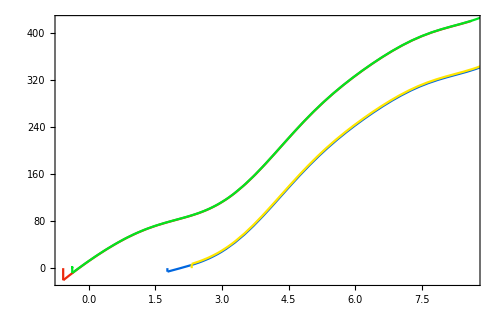

```mathematica
Block[{θx=0.5,fc,saddles,classifiedsaddles,trajectoryContour,scheme="2ω",part=Re,px=3},
fc=fastFieldConfigθ[θx];
saddles=findSaddles[fc,testtargetconfig][px];
classifiedsaddles=classifySaddles[fc,testtargetconfig][saddles,"2ω"];

Show[
Table[
With[{ωts=seed[[1]],label=seed[[2]]},
trajectoryContour[s_]:=If[s<Im[ωts],ωts-ⅈ s,Re[ωts]+(s-Im[ωts])];
ParametricPlot[
Tooltip[
{
part[trajectoryContour[s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[s]]]
}
,{label,px}]
,{s,0,Im[ωts]+(30°)/((Association@@testfieldconfig)[["ω"]])}
,PlotStyle->Directive[LabelColors[label]]
]
]
,{seed,classifiedsaddles}]

(*,PlotRange->All*)
,Frame->True
,ImageSize->500
,AspectRatio->1/1.6
]

]
```

### plot for all momenta

{-0.029701+1.04967 ⅈ,B}

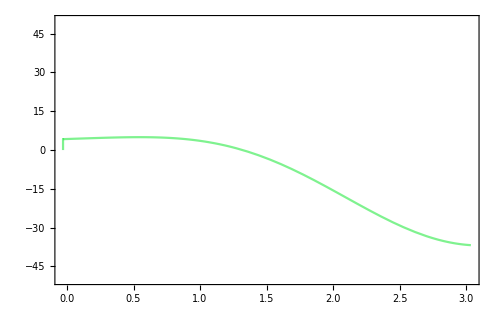

```mathematica
Block[{θx=π/4,fc,saddles,classifiedsaddlespp,classifiedsaddlespm,classifiedsaddlesp0,trajectoryContour,scheme="2ω",part=Re,label="B",pextra=0.1},
fc=fastFieldConfigθ[θx];
classifiedsaddlespp=Select[classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][pextra],"2ω"],#[[2]]==label&][[1]];
classifiedsaddlespm=Select[classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][-pextra],"2ω"],#[[2]]==label&][[1]];
classifiedsaddlesp0=Select[classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][0],"2ω"],#[[2]]==label&][[1]];
trajectoryContour[ωts_,s_]:=If[s<Im[ωts],ωts-ⅈ s,Re[ωts]+(s-Im[ωts])];
Print[classifiedsaddlespp];
Show[{
(*With[{ωts=classifiedsaddlesp0[[1]],px=0},
ParametricPlot[
{
part[trajectoryContour[ωts,s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[ωts,s]]]
}
,{s,0,Im[ωts]+(30°)/((Association@@testfieldconfig)[["ω"]])}
,PlotStyle->Directive[LabelColors[label]]
]
]
,*)

With[{ωts=classifiedsaddlespp[[1]],px=+pextra},
ParametricPlot[
{
part[trajectoryContour[ωts,s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[ωts,s]]]
}
,{s,0,Im[ωts]+(10°)/((Association@@testfieldconfig)[["ω"]])}
,PlotStyle->Directive[LabelColors[label],Opacity[0.5]]
]
],

(*With[{ωts=classifiedsaddlespm[[1]],px=-pextra},

ParametricPlot[
{
part[trajectoryContour[ωts,s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[ωts,s]]]
}
,{s,0,Im[ωts]+(30°)/((Association@@testfieldconfig)[["ω"]])}
,PlotStyle->Directive[LabelColors[label],Opacity[0.5]]
]
],*)
Graphics[{}]
}

,PlotRange->{Full,{-50,50}}
,Frame->True
,ImageSize->500
,AspectRatio->1/1.6
]
]
```

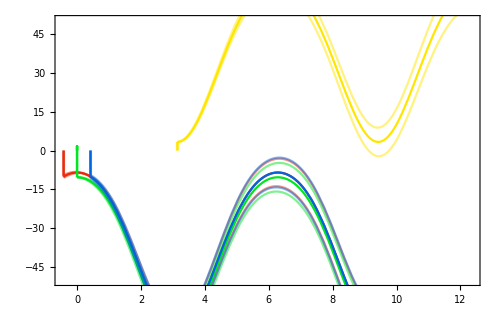

```mathematica
Block[{θx=0.4,fc,classifiedsaddlespp,classifiedsaddlespm,classifiedsaddlesp0,trajectoryContour,scheme="2ω",part=Re,pextra=0.05},
fc=fastFieldConfigθ[θx];
trajectoryContour[ωts_,s_]:=If[s<Im[ωts],ωts-ⅈ s,Re[ωts]+(s-Im[ωts])];
classifiedsaddlespp=classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][pextra],"2ω"];
classifiedsaddlespm=classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][-pextra],"2ω"];
classifiedsaddlesp0=classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][0],"2ω"];

Show[{
Table[
Block[{saddlepp,saddlepm,saddlep0},
saddlepp=Select[classifiedsaddlespp,#[[2]]==label&][[1]];
saddlepm=Select[classifiedsaddlespm,#[[2]]==label&][[1]];
saddlep0=Select[classifiedsaddlesp0,#[[2]]==label&][[1]];

{With[{ωts=saddlep0[[1]],px=0},
ParametricPlot[
{part[trajectoryContour[ωts,s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[ωts,s]]]}
,{s,0,Im[ωts]+(30°)/((Association@@testfieldconfig)[["ω"]])}
,PlotStyle->Directive[LabelColors[label]]
]
],

With[{ωts=saddlepp[[1]],px=+pextra},
ParametricPlot[{
part[trajectoryContour[ωts,s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[ωts,s]]]}
,{s,0,Im[ωts]+(30°)/((Association@@testfieldconfig)[["ω"]])}
,PlotStyle->Directive[LabelColors[label],Opacity[0.5]]
]
],

With[{ωts=saddlepm[[1]],px=-pextra},
ParametricPlot[
{part[trajectoryContour[ωts,s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[ωts,s]]]}
,{s,0,Im[ωts]+(30°)/((Association@@testfieldconfig)[["ω"]])}
,PlotStyle->Directive[LabelColors[label],Opacity[0.5]]
]
]}

],{label,{"A","B","C","D"}}],

Graphics[{}]
}

,PlotRange->{Full,{-50,50}}
,Frame->True
,ImageSize->500
,AspectRatio->1/1.6
]
]
```

### making bands for other p values

```mathematica
makepextraCurve[fc_,label_,pextra_,traveltime_]:=Module[{ω,saddles,classifiedsaddlespp,classifiedsaddlespm,classifiedsaddlesp0,trajectoryContour,scheme="2ω",part=Re
(*,label="B",pextra=0.1,traveltime=(5°)/((Association@@testfieldconfig)[["ω"]])*),
ωtspp,ωtspm,
tunnel1,tunnel2,traj1,traj2,finish,start,starttunnelexit
,makeLine,curve,curve2},
(*fc=fastFieldConfigθ[θx];*)
(*ω=(Association@@testfieldconfig)[["ω"]];*)
classifiedsaddlespp=Select[classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][pextra],"2ω"],#[[2]]==label&][[1]];
classifiedsaddlespm=Select[classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][-pextra],"2ω"],#[[2]]==label&][[1]];
(*classifiedsaddlesp0=Select[classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][0],"2ω"],#[[2]]==label&][[1]];*)
ωtspp=classifiedsaddlespp[[1]];
ωtspm=classifiedsaddlespm[[1]];
makeLine[plot_]:=Cases[plot,Line[a_]:>a,Infinity][[1]];

traj1=ParametricPlot[
{part[Re[ωtspp]+(s-Im[ωtspp])],
part[trajectoryFromConfig[fc][+pextra,ωtspp,Re[ωtspp]+(s-Im[ωtspp])]]
},
{s,Im[ωtspp],Im[ωtspp]+traveltime}
];

finish=Graphics[Line[{
{part[Re[ωtspp]+traveltime],part[trajectoryFromConfig[fc][+pextra,ωtspp,Re[ωtspp]+traveltime]]},
{part[Re[ωtspm]+traveltime],part[trajectoryFromConfig[fc][-pextra,ωtspm,Re[ωtspm]+traveltime]]}
}]];

traj2=ParametricPlot[
{part[Re[ωtspm]+(s-Im[ωtspm])],
part[trajectoryFromConfig[fc][-pextra,ωtspm,Re[ωtspm]+(s-Im[ωtspm])]]
},{s,Im[ωtspm],Im[ωtspm]+traveltime}];

starttunnelexit=Graphics[Line[{
{Re[ωtspp],part[trajectoryFromConfig[fc][+pextra,ωtspp,Re[ωtspp]]]},
{Re[ωtspm],part[trajectoryFromConfig[fc][-pextra,ωtspm,Re[ωtspm]]]}
}]];

curve=FilledCurve[Line[Join[
makeLine[traj1],makeLine[finish],makeLine[traj2]//Reverse,makeLine[starttunnelexit]//Reverse
]
]]

(*Graphics[{Orange,curve},AspectRatio->1/2]*)

]
```

```mathematica
Options[makepextraCurve]={endtime->12};Protect[endtime];
```

```mathematica
endtime
```

endtime

```mathematica
makepextraCurve2[fc_,label_,pextra_,endtime_]:=Module[{ω,saddles,classifiedsaddlespp,classifiedsaddlespm,classifiedsaddlesp0,trajectoryContour,scheme="2ω",part=Re
(*,label="B",pextra=0.1,traveltime=(5°)/((Association@@testfieldconfig)[["ω"]])*),
ωtspp,ωtspm,
tunnel1,tunnel2,traj1,traj2,finish,start,starttunnelexit
,makeLine,curve,curve2},
(*fc=fastFieldConfigθ[θx];*)
(*ω=(Association@@testfieldconfig)[["ω"]];*)
classifiedsaddlespp=Select[classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][pextra],"2ω"],#[[2]]==label&][[1]];
classifiedsaddlespm=Select[classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][-pextra],"2ω"],#[[2]]==label&][[1]];
(*classifiedsaddlesp0=Select[classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][0],"2ω"],#[[2]]==label&][[1]];*)
ωtspp=classifiedsaddlespp[[1]];
ωtspm=classifiedsaddlespm[[1]];
makeLine[plot_]:=Cases[plot,Line[a_]:>a,Infinity][[1]];

traj1=ParametricPlot[
{part[Re[ωtspp]+(s-Im[ωtspp])],
part[trajectoryFromConfig[fc][+pextra,ωtspp,Re[ωtspp]+(s-Im[ωtspp])]]
},
{s,Im[ωtspp],endtime+Im[ωtspp]-Re[ωtspp]}
];

finish=Graphics[Line[{
{part[endtime],part[trajectoryFromConfig[fc][+pextra,ωtspp,endtime]]},
{part[endtime],part[trajectoryFromConfig[fc][-pextra,ωtspm,endtime]]}
}]];

traj2=ParametricPlot[
{part[Re[ωtspm]+(s-Im[ωtspm])],
part[trajectoryFromConfig[fc][-pextra,ωtspm,Re[ωtspm]+(s-Im[ωtspm])]]
},{s,Im[ωtspm],Im[ωtspm]+endtime-Re[ωtspp]}];

starttunnelexit=Graphics[Line[{
{Re[ωtspp],part[trajectoryFromConfig[fc][+pextra,ωtspp,Re[ωtspp]]]},
{Re[ωtspm],part[trajectoryFromConfig[fc][-pextra,ωtspm,Re[ωtspm]]]}
}]];

curve=FilledCurve[Line[Join[
makeLine[traj1],makeLine[finish],makeLine[traj2]//Reverse,makeLine[starttunnelexit]//Reverse
]
]]

(*Graphics[{Orange,curve},AspectRatio->1/2]*)

]
```

#### test

```mathematica
Block[{θx=π/4,fc,classifiedsaddlespp,classifiedsaddlespm,classifiedsaddlesp0,trajectoryContour,scheme="2ω",part=Re,pextra=0.05,traveltime},
fc=fastFieldConfigθ[θx];
trajectoryContour[ωts_,s_]:=If[s<Im[ωts],ωts-ⅈ s,Re[ωts]+(s-Im[ωts])];
classifiedsaddlespp=classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][pextra],"2ω"];
classifiedsaddlespm=classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][-pextra],"2ω"];
classifiedsaddlesp0=classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][0],"2ω"];
traveltime=(30°)/((Association@@testfieldconfig)[["ω"]]);
Show[{
Table[
Block[{saddlepp,saddlepm,saddlep0},
saddlepp=Select[classifiedsaddlespp,#[[2]]==label&][[1]];
saddlepm=Select[classifiedsaddlespm,#[[2]]==label&][[1]];
saddlep0=Select[classifiedsaddlesp0,#[[2]]==label&][[1]];

{With[{ωts=saddlep0[[1]],px=0},
ParametricPlot[
{part[trajectoryContour[ωts,s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[ωts,s]]]}
,{s,0,Im[ωts]+traveltime}
,PlotStyle->Directive[LabelColors[label]]
]
],
Graphics[{Directive[LabelColors[label],Opacity[0.3]],makepextraCurve2[fc,label,pextra,12]}]
(*With[{ωts=saddlepp[[1]],px=+pextra},
ParametricPlot[{
part[trajectoryContour[ωts,s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[ωts,s]]]}
,{s,0,Im[ωts]+traveltime}
,PlotStyle->Directive[LabelColors[label],Opacity[0.5]]
]
],*)

(*With[{ωts=saddlepm[[1]],px=-pextra},
ParametricPlot[
{part[trajectoryContour[ωts,s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[ωts,s]]]}
,{s,0,Im[ωts]+traveltime}
,PlotStyle->Directive[LabelColors[label],Opacity[0.5]]
]
]*)

}

],{label,{"A","B","C","D"}}],



Graphics[{}]
}

,PlotRange->{Full,{-50,50}}
,Frame->True
,ImageSize->500
,AspectRatio->1/1.6
]
]
```

-Graphics-

### final plot

#### Settings

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"
    \\usepackage{amssymb}
    \\usepackage[T1]{fontenc}
    \\usepackage{xcolor}
    \\usepackage{siunitx}
    \\usepackage{MnSymbol}
    "}];
```

```mathematica
columnWidth=246;
```

```mathematica
piify[q_,"TeX"]:=StringReplace[
ToString[Numerator[q]]<>"\\pi/"<>ToString[Denominator[q]]
,{"/1"->"","1\\pi"->"\\pi","0\\pi"->"0"}]
```

```mathematica
fsS=8;fsM=9;fsL=10;
mygrey=GrayLevel[0.5];
```

#### plot

```mathematica
fig=Block[{θx=π/4,fc,classifiedsaddlespp,classifiedsaddlespm,classifiedsaddlesp0,trajectoryContour,scheme="2ω",part=Re,pextra=0.05,traveltime,endtime},
fc=fastFieldConfigθ[θx];
trajectoryContour[ωts_,s_]:=If[s<Im[ωts],ωts-ⅈ s,Re[ωts]+(s-Im[ωts])];
(*classifiedsaddlespp=classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][pextra],"2ω"];
classifiedsaddlespm=classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][-pextra],"2ω"];*)
classifiedsaddlesp0=classifySaddles[fc,testtargetconfig][findSaddles[fc,testtargetconfig][0],"2ω"];
traveltime=(30°)/((Association@@testfieldconfig)[["ω"]]);
endtime=7/2 π;
Show[{
Table[
Block[{saddlep0},
saddlep0=Select[classifiedsaddlesp0,#[[2]]==label&][[1,1]];

{With[{ωts=saddlep0,px=0},
ParametricPlot[
{part[trajectoryContour[ωts,s]],
part[trajectoryFromConfig[fc][px,ωts,trajectoryContour[ωts,s]]]}
,{s,0,Im[ωts]+endtime-Re[ωts]}
,PlotStyle->Directive[LabelColors[label]]
]
],
Graphics[{Directive[LabelColors[label],Opacity[0.3]],makepextraCurve2[fc,label,pextra,endtime]}]
}
],{label,{"A","B","C","D"}}],

Graphics[{White,FilledCurve[{
{Line[ImageScaled/@{{-0.1,-0.1},{1.1,-0.1},{1.1,1.1},{-0.1,1.1}}]},
{Line[Scaled/@({{0,0},{1,0},{1,1},{0,1}})]}}]}],

Graphics[{
Table[Inset[MaTeX[piify[qx,"TeX"],FontSize->fsM],{qx π,-60}],{qx,0,7/2,1}],
Inset[MaTeX["\\mathrm{Re}(\\omega t)",FontSize->fsM],Scaled[{0.5,-0.15}]]}],

Graphics[{
Table[Inset[Graphics[MaTeX[qy,FontSize->fsM]],{-π/2-0.25,qy },Scaled[{1,0.5}]],{qy,-50,50,25}],
Inset[Rotate[MaTeX["\\mathrm{Re}(x(t))",FontSize->fsM],90°],Scaled[{-0.12,0.5}]]
}
],

Graphics[{
Inset[Text[Style["A",FontSize->fsM,FontColor->LabelColors[["A"]]]],{-0.9,-15}],Inset[Text[Style["B",FontSize->fsM,FontColor->LabelColors[["B"]]]],{0.5,12}],Inset[Text[Style["C",FontSize->fsM,FontColor->LabelColors[["C"]]]],{0.9,-15}],Inset[Text[Style["D",FontSize->fsM,FontColor->Darker[LabelColors[["D"]],0.08]]],{π,12}]
}],

Graphics[{}]
}

,Frame->True,FrameLabel->None,FrameStyle->Black
,PlotRange->{{-π/2,7/2 π},{-55,55}}
,PlotRangeClipping->False
,AspectRatio->1/1.6
,ImageSize->(Automatic->200)
,Axes->True,Method->{"AxesInFront"->False},AxesStyle->Black
,FrameTicks->{{{# ,"",{0.015,0}}&/@Range[-50,50,25],None},
{Join[{# π,"",{0.01,0}}&/@Range[-1,8/2,1/4],(*small x*)
{# π,"",{0.015,0}}&/@Range[-1,8/2,1/2]],None}}
(*,ImagePadding->{{35,5},{30,5}}*)
,ImagePadding->{{Scaled[0.062],Scaled[0.003]},{Scaled[0.05],Scaled[0.003]}}
,PlotRangePadding->None
]
]
```

-Graphics-

#### test in greyscale

```mathematica
test=-Graphics-;
```

```mathematica
ColorConvert[test,"Grayscale"]
```

-Graphics-

#### Export

```mathematica
SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"]
```

```mathematica
Export[
FileNameJoin[
{"/home/anne/OneDrive/Paper 1 - Tunnelling without barrier/overleaf/",
"figtrajectories.pdf"}],fig,ImageResolution->600,ImageSize->columnWidth-1]
```

/home/anne/OneDrive/Paper 1 - Tunnelling without barrier/overleaf/figtrajectories.pdf